```mathematica
f[x_]:=(E^x)Sin[x]
```

```mathematica
f[x_,y_]:=Sin[x^2+y^2]
```

```mathematica
f[x_,y_]:=ArcTan[y/x]
```

```mathematica
∑_(i=1)^100 i
```

5050

```mathematica
∑_(i=1)^n (i^2)
```

1/6 n (1+n) (1+2 n)

```mathematica
∑_(i=1)^50 (2i-1)
```

2500

```mathematica
∑_(i=0)^∞ (1/2)^i
```

2

```mathematica
∑_(i=1)^7 ∑_(j=1)^i j
```

84

```mathematica
∏_(i=1)^6 i^2
```

518400

```mathematica
∏_(i=1)^4 ∏_(j=1)^i j*2
```

294912

```mathematica
FormulaOfSummation[x_]:=∑_(i=1)^n i^x
```

```mathematica
FormulaOfSummation[1]
```

1/2 n (1+n)

Set::write: "Tag Plus in 2 is Protected. (*ButtonBox[

```mathematica
FormulaOfSummation[2]
```

1/6 n (1+n) (1+2 n)

```mathematica
FormulaOfSummation[3]
```

1/4 n^2 (1+n)^2

```mathematica
Solve[x^2+9*x+2==0,x]
```

{{x→1/2 (-9-√73)},{x→1/2 (-9+√73)}}

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[a*x^3+b*x+d==0,x]
```

{{x→-((2/3)^(1/3) b)/(-9 a^2 d+√3 √(4 a^3 b^3+27 a^4 d^2))^(1/3)+(-9 a^2 d+√3 √(4 a^3 b^3+27 a^4 d^2))^(1/3)/(2^(1/3) 3^(2/3) a)},{x→((1+ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 a^2 d+√3 √(4 a^3 b^3+27 a^4 d^2))^(1/3))-((1-ⅈ √3) (-9 a^2 d+√3 √(4 a^3 b^3+27 a^4 d^2))^(1/3))/(2 2^(1/3) 3^(2/3) a)},{x→((1-ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 a^2 d+√3 √(4 a^3 b^3+27 a^4 d^2))^(1/3))-((1+ⅈ √3) (-9 a^2 d+√3 √(4 a^3 b^3+27 a^4 d^2))^(1/3))/(2 2^(1/3) 3^(2/3) a)}}

```mathematica
NSolve[x^5+16*x^4+7*x^3+17*x^2+11*x+5==0,x]
```

{{x→-15.6187},{x→-0.386706-0.39778 ⅈ},{x→-0.386706+0.39778 ⅈ},{x→0.196058-1.00086 ⅈ},{x→0.196058+1.00086 ⅈ}}

```mathematica
Solve[Sin[ArcCos[x^2-x]]==1,x]
```

{{x→0},{x→1}}

```mathematica
Solve[{5*x^2+6*y^2==9,x+y==1},{x,y}]
```

{{x→1/11 (6-√69),y→1/11 (5+√69)},{x→1/11 (6+√69),y→1/11 (5-√69)}}

```mathematica
Solve[{x+y+z==9,x+4*y==4,2*x+3*y+z==9},{x,y,z}]
```

{{x→-4,y→2,z→11}}

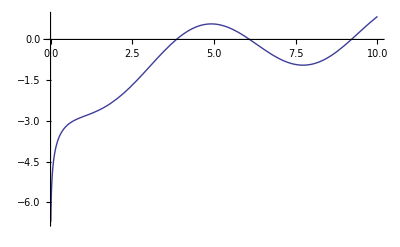

```mathematica
Plot[{Log[x]-Sin[x]-2},{x,0,10}]
```

```mathematica
FindRoot[{Log[x]-Sin[x]-2==0},{x,4}]
```

{x→3.85128}

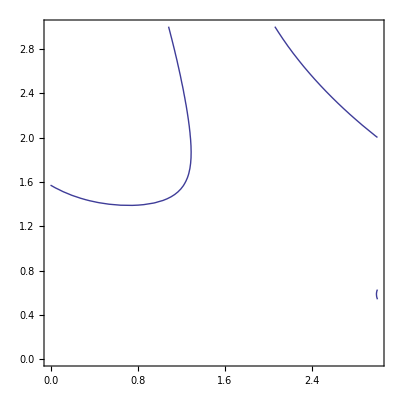

```mathematica
a=ContourPlot[{Sin[x*y]==Sin[x]+Cos[y]},{x,0,3},{y,0,3}]
```

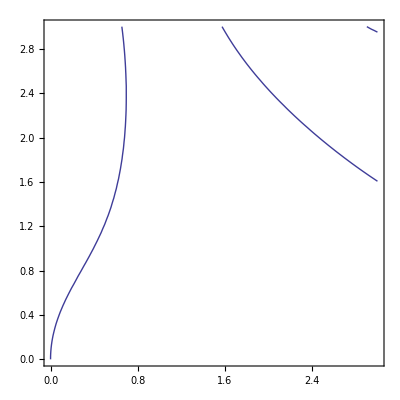

```mathematica
b=ContourPlot[{Cos[x*y]==Sin[x]+Cos[y]},{x,0,3},{y,0,3}]
```

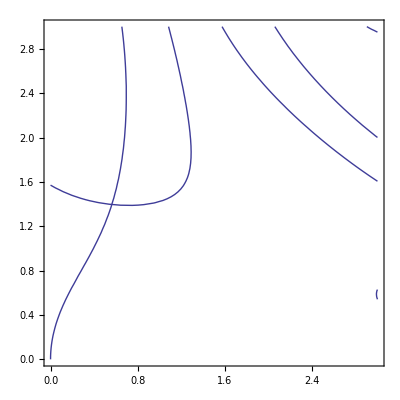

```mathematica
Show[a,b]
```

```mathematica
FindRoot[{{Sin[x*y]==Sin[x]+Cos[y]},{Cos[x*y]==Sin[x]+Cos[y]}},{x,0.6},{y,1.4}]
```

{x→0.562547,y→1.39615}